# 频率派

## 统计推断

## 中心极限定理

### 离散随机变量

```mathematica
(*每次抛n枚骰子，一共抛k次*)
diceMean[k_,n_]:=Show[Histogram[#,{.2},"PDF"],SmoothHistogram@#]&@(Mean/@RandomInteger[{1,6},{k,n}])
```

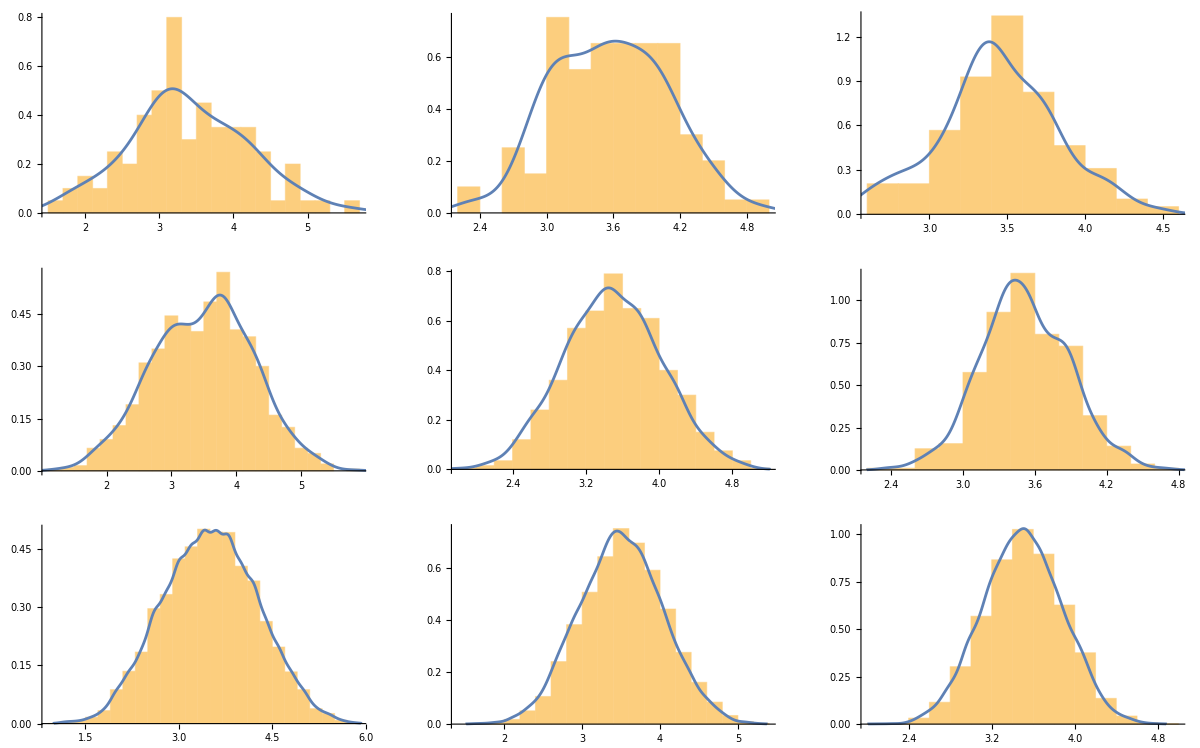

```mathematica
diceMean@@@Flatten[#,1]&@Outer[{#1,#2}&,{100,1000,10000},{5,10,20}]//ArrayReshape[#,{3,3}]&//GraphicsGrid
```

### 连续随机变量

```mathematica
distMean[dist_,k_,n_]:=Show[Histogram[#,{.2},"PDF"],SmoothHistogram@#]&@(Mean/@RandomVariate[dist,{k,n}])
```

随机变量服从“双峰”分布

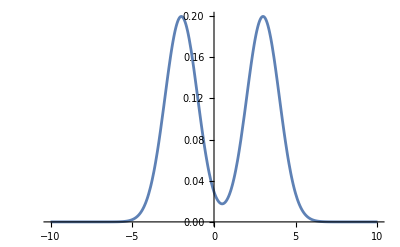

```mathematica
doublePeakDist=MixtureDistribution[{1/2,1/2},{NormalDistribution[-2,1],NormalDistribution[3,1]}];
Plot[PDF[doublePeakDist,x],{x,-10,10},PlotTheme->"Minimal"]
```

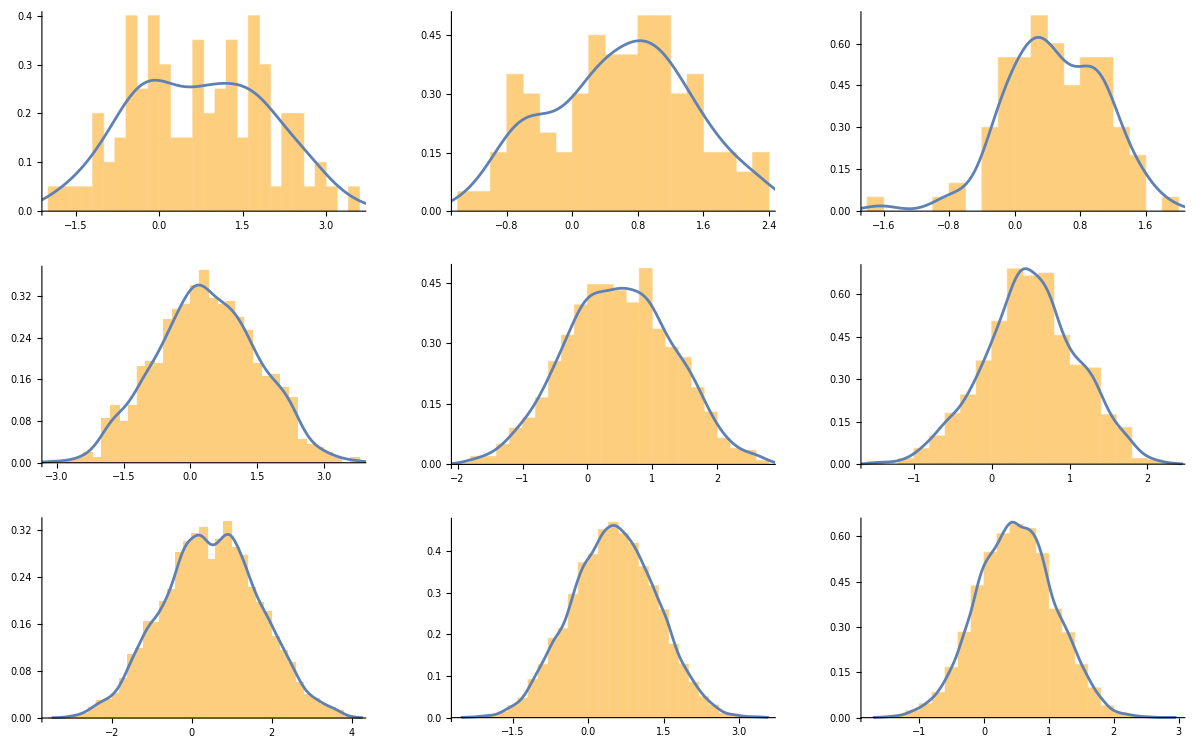

```mathematica
distMean[doublePeakDist,#1,#2]&@@@Flatten[#,1]&@Outer[{#1,#2}&,{100,1000,10000},{5,10,20}]//ArrayReshape[#,{3,3}]&//GraphicsGrid
```

## 最大似然

### 伯努利分布

```mathematica
Likelihood[BernoulliDistribution[θ],{x1,x2,x3,x4,x5}]
```

Piecewise[{{(1-θ)^(5-x1-x2-x3-x4-x5) θ^(x1+x2+x3+x4+x5), 0≤x1≤1&&0≤x2≤1&&0≤x3≤1&&0≤x4≤1&&0≤x5≤1}, {0, True}}]

令  可得

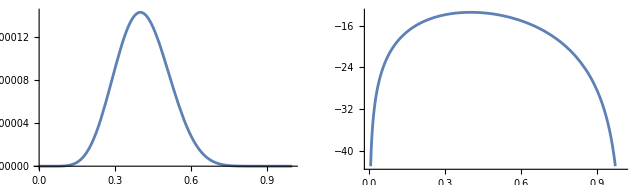

```mathematica
l[s_,n_,theta_]:=theta^s(1-theta)^(n-s)
{Plot[l[8,20,theta],{theta,0,1}],Plot[Log@l[8,20,theta],{theta,0,1}]}//GraphicsRow
```

```mathematica
Solve[D[Log@l[s,n,theta],theta]==0,theta]
```

{{theta→s/n}}

### 正态分布

```mathematica
logL[μ_,σ_]:=LogLikelihood[NormalDistribution[μ,σ],{-2.5,-5,1,3.5,-4,1.5,5.5}]
```

```mathematica
sol=Solve[{D[logL[μ,σ],μ]==0,D[logL[μ,σ],σ]==0},{μ,σ},Assumptions->σ>0]//Quiet//Flatten
```

{μ→0,σ→3.64496}

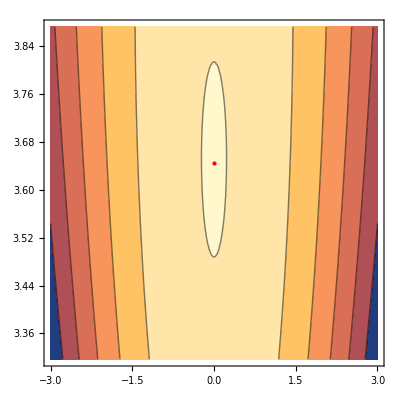

```mathematica
{ContourPlot[logL[μ,σ],{μ,-3,3},{σ,Sqrt@11,Sqrt@15},PlotPoints->50,Epilog->{Red,PointSize[Large],Point[{μ,σ}/. sol]}],Show[Plot3D[logL[μ,σ],{μ,-3,3},{σ,Sqrt@11,Sqrt@15}],Graphics3D[{Red,PointSize[Large],Point[{μ,σ,logL[μ,σ]}/. sol]}]]}//GraphicsRow
```

## 概率密度估计

## 可视化“叠加”

```mathematica
kernelPlot[data_List,h_]:=Module[{kernels,kernelPlots,dataRug},
kernels=NormalDistribution[#,h]&/@data;
kernelPlots=Show[Table[Plot[1/Length@data PDF[i,x],{x,-10,15},PlotRange->All,PlotStyle->{Red,Dashed}],{i,kernels}]];
dataRug=Show[Table[Graphics[{Black,Line[{{i,0},{i,1/Length@data PDF[NormalDistribution[0,h],0]}}]}],{i,data}]];
Show[SmoothHistogram[data,{h,"Gaussian"},Frame->True,Axes->None,PlotStyle->Thick,PlotRange->{{-7,11},All}],kernelPlots,dataRug]
]
```

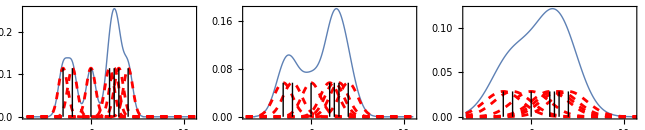

```mathematica
kernelPlot[{-3,-2,0,2,2.5,3,4},#]&/@{.5,1,2}//GraphicsRow
```

## 带宽

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];
```

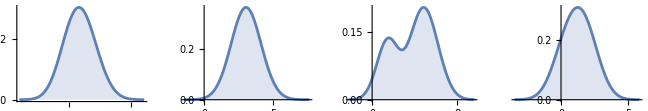

```mathematica
SmoothHistogram[#,1,"PDF",Filling->Axis]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//GraphicsRow
```

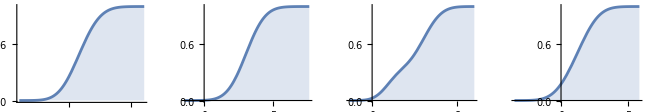

```mathematica
SmoothHistogram[#,1,"CDF",Filling->Axis]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//GraphicsRow
```

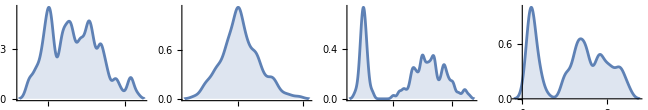

```mathematica
SmoothHistogram[#,.1,"PDF",Filling->Axis]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//GraphicsRow
```

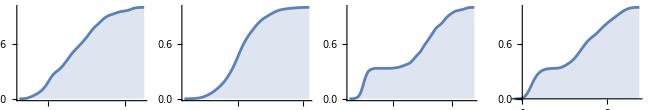

```mathematica
SmoothHistogram[#,.1,"CDF",Filling->Axis]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//GraphicsRow
```

## 核函数

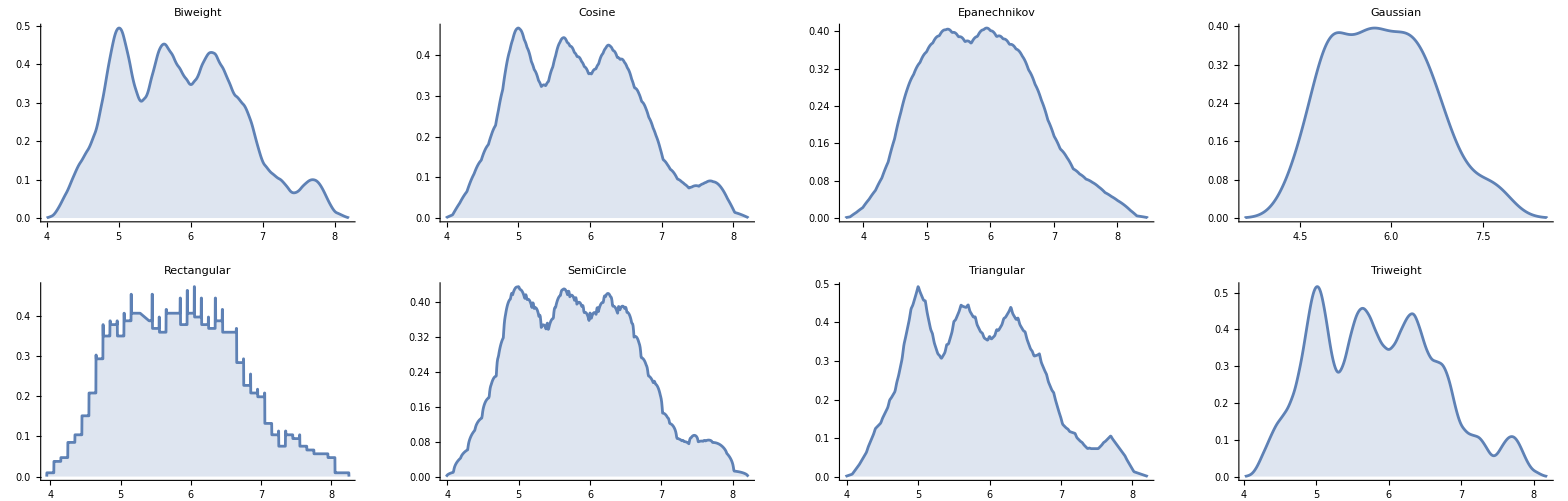

```mathematica
Table[SmoothHistogram[sepalLength,{Automatic,i},Filling->Axis,PlotLabel->i,Ticks->None],{i,{"Biweight","Cosine","Epanechnikov","Gaussian","Rectangular","SemiCircle","Triangular","Triweight"}}]//ArrayReshape[#,{2,4}]&//GraphicsGrid
```

## 二元 KDE

```mathematica
#[Transpose@{sepalLength,sepalWidth},Mesh->20]&/@{SmoothHistogram3D,SmoothDensityHistogram}//GraphicsRow
```

-Graphics-